# Probability of generating an intermediate configuration

12/29/2023 呂承儫

	In GEMC for solid phase transition. the condition of detailed balance is 
-Graphics-
N(o) is the probability of finding an old configuration, o.
Pgen(o->n’) is the probability of generating an intermediate configuration, n’, from an old configuration, o.
Pcorrect(n’->n) is the probability of generating an ‘annealing’ configuration, n.

	In this notebook I will show that Pgen(o->n’)=1/(2#o), #o is the atom number in a unit cell of configuration o.

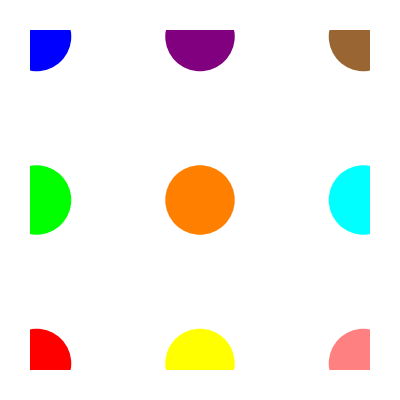

```mathematica
nLat=3;
pointUC=Flatten[Table[{i,j},{i,0,nLat-1},{j,0,nLat-1}],1];
lat0={{nLat,0},{0,nLat}};
colors={Red,Green,Blue,Yellow,Orange,Purple,Pink,Cyan,Brown};
unit=MapThread[{#1,PointSize[0.1],Point[#2]}&,{colors,pointUC}];
Graphics[MapThread[{#1,PointSize[0.3],Point[#2]}&,{colors,pointUC}]]
(*unitcell structure*)
```

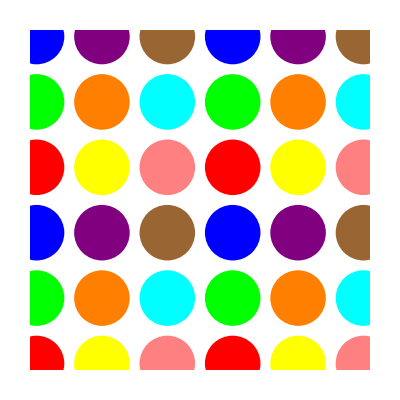

```mathematica
xdir=MapThread[{#1,PointSize[0.1],Point[#2+lat0[[1]]]}&,{colors,pointUC}];
ydir=MapThread[{#1,PointSize[0.1],Point[#2+lat0[[2]]]}&,{colors,pointUC}];
xydir=MapThread[{#1,PointSize[0.1],Point[#2+lat0[[1]]+lat0[[2]]]}&,{colors,pointUC}];
Graphics[Join[unit,xdir,ydir,xydir]]  
(*supercell 2X2*)
```

```mathematica
nlat=3;
pointUC=Flatten[Table[{i,j,k},{i,0,nLat-1},{j,0,nLat-1},{k,0,nLat-1}],2];
lat0={{nLat,0,0},{0,nLat,0},{0,0,nLat}};
```